# Yang–Mills scattering with graviton emission

A^a(p_1)+A^b(p_2)⟶A^c(p_3)+h(p_4)

Tree-level scattering of two massless SU(N) gauge fields into a gauge field and a graviton. This example isolates a mixed non-Abelian interaction: the amplitude is proportional to gₛ κ fᵃᵇᶜ and vanishes when gₛ = 0. Start in a fresh kernel and evaluate from top to bottom. D and N stay symbolic in the initial calculation. The final section specialises the external states to four-dimensional helicities. No colour averages or cross sections are calculated. FeynCalc and patched FeynArts are sufficient; FORM is not needed.

## 1. Load FeynGrav and the model

```mathematica
$LoadAddOns={"FeynArts"};<<"FeynGrav`";
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynGrav 4.2.0 (development)

Feynman rules for gravity and matter, with FeynCalc notation and FORM support through CalcFormConverter.

The default libraries include cubic and quartic graviton vertices and scalar, Dirac fermion and vector interactions with up to two gravitons. Use the FeynGravImport* commands to load additional libraries.

FeynArts supported models

• Pure general relativity

• Scalar field with a potential minimally coupled to gravity

• Scalar field with a non-minimal kinetic coupling

• Einstein-scalar-Gauss-Bonnet model

• SU(N) Yang-Mills field coupled to gravity

The supplied models retain interactions through order κ^2 per vertex. Use matching Model and GenericModel names with FeynCalc-patched FeynArts in a fresh kernel. Models are not initialised automatically.

Evaluate FeynGravCommands[] to list available commands, FeynGravConventions[] to inspect conventions and current settings, and FeynGravHowToCite[] for citation guidance.

```mathematica
model="GR-SU-N-Yang-Mills";InitializeModel[model,GenericModel->model];
```

loading generic model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/GR-SU-N-Yang-Mills/GR-SU-N-Yang-Mills.gen

> $GenericMixing is OFF

generic model {GR-SU-N-Yang-Mills} initialized

loading classes model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/GR-SU-N-Yang-Mills/GR-SU-N-Yang-Mills.mod

> 6 particles (incl. antiparticles) in 4 classes

> $CounterTerms are ON

> 16 vertices

classes model {GR-SU-N-Yang-Mills} initialized

The model has a massless adjoint gauge field V[1], a graviton T[1], and distinct gravitational and Yang–Mills ghost sectors. Ghosts do not occur in these physical external-state trees. The fixed source gauges are GaugeFixingEpsilon = 2 and GaugeFixingEpsilonSUNYM = −1.

## 2. Generate and display the four diagrams

```mathematica
topologies=CreateTopologies[0,2->2,Adjacencies->{3,4,5,6}];insertions=InsertFields[topologies,{V[1],V[1]}->{V[1],T[1]},Model->model,GenericModel->model,InsertionLevel->{Classes}];
```

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

in total: 4 Classes insertions

There is one hAAA contact and three gauge-field exchanges in the s, t and u channels. All four contributions are required for the gauge-field Ward identities. Their common coupling order is gₛ κ. The model cutoff is κ.b2 per vertex; it is not a cutoff on the total order of an arbitrary diagram.

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

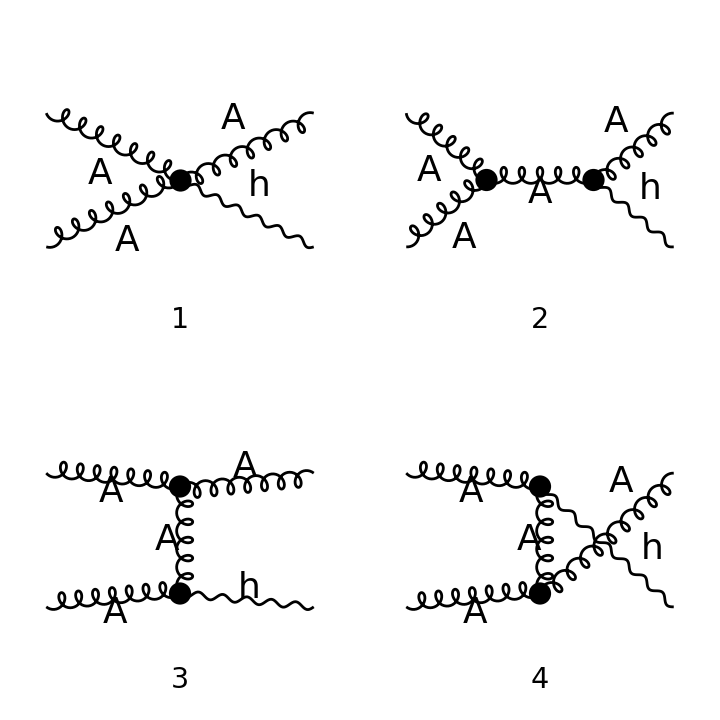

```mathematica
Paint[insertions,ColumnsXRows->{2,2},Numbering->Simple,AutoEdit->False,DisplayFunction->Function[sheet,diagramPainting=sheet;diagramSheets=Render[sheet,ImageSize->{720,720}]]];Column[diagramSheets]
```

## 3. Fix the massless on-shell kinematics

The momenta p₁ and p₂ are incoming; p₃ and p₄ are outgoing. Thus p₁ + p₂ = p₃ + p₄ and s + t + u = 0. SetMandelstam fixes momentum scalar products but does not remove p₄ from products with polarisation vectors. The helper below applies that conservation relation explicitly and uses s and t as the independent invariants.

```mathematica
FCClearScalarProducts[];SetMandelstam[s,t,u,p1,p2,-p3,-p4,0,0,0,0];simplifyOnShell[expr_,stateRules_:{}]:=Factor[Together[ExpandScalarProduct[Contract[expr]/.Momentum[p4,D]->Momentum[p1+p2-p3,D]]/.stateRules/.u->-s-t]];
```

## 4. Construct the tensor amplitude and retain its colour factor

```mathematica
raw=CreateFeynAmp[insertions,Truncated->True,MomentumConservation->True,PreFactor->1];tensorDiagrams=FCFAConvert[raw,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LorentzIndexNames->{μ,ν,ρ,α,β},ChangeDimension->D,List->True,SMP->False,DropSumOver->False];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

in total: 4 Classes amplitudes

PreFactor -> 1 retains the source normalisation; FeynArts supplies diagram weights. MomentumConservation -> True fixes internal routing. Truncated -> True leaves three free gauge-field indices and two graviton indices. We retain all colour sums during conversion, remove only external-state sum markers, and verify that every internal colour index occurs exactly twice in each monomial before using FeynCalc’s repeated-index contraction. The result is a fixed-colour amplitude, not a colour average.

```mathematica
fixedColour[expr_]:=Module[{amplitude,sums,index,terms},amplitude=expr/.SumOver[_,_,External]->1;sums=DeleteDuplicates[Cases[amplitude,_SumOver,∞]];Do[index=First[sum];amplitude=amplitude/.sum->1;terms=If[Head[Expand[amplitude]]===Plus,List@@Expand[amplitude],{Expand[amplitude]}];If[!AllTrue[terms,Count[#1,index,∞]===2&],Print["Unexpected internal colour sum; stop and inspect the diagram."];Abort[]],{sum,sums}];SUNSimplify[amplitude,SUNNToCACF->False]];tensorDiagrams=fixedColour/@tensorDiagrams/.{YangMillsCoupling->gs,SUNIndex[Glu1]->SUNIndex[a],SUNIndex[Glu2]->SUNIndex[b],SUNIndex[Glu3]->SUNIndex[c]};tensorAmplitude=FeynAmpDenominatorExplicit[Total[tensorDiagrams]]/ⅈ;contactAmplitude=FeynAmpDenominatorExplicit[Total[Select[tensorDiagrams,FreeQ[#1,FeynAmpDenominator]&]]]/ⅈ;colourFactor=FCI[SUNF[a,b,c]];
```

The native diagrams give iℳ; division by I defines ℳ in the same convention as the preceding examples. No additional symmetry factor is inserted. Keeping tensorAmplitude before attaching physical polarisations is essential for the Ward checks below.

## 5. Calculate and present the physical amplitude

Incoming gauge fields use ε(p₁) and ε(p₂); the outgoing gauge field uses ε*(p₃). The outgoing graviton uses the factorised conjugate tensor ε*ᵅ(p₄) ε*ᵝ(p₄). The underlying graviton vector is transverse and null, so the tensor is transverse and traceless. This is a convenient family of states, not a complete D-dimensional polarisation basis. No D = 4 limit is taken. The labels I and −I specify conjugation, not helicity.

```mathematica
polarisations={Polarization[p1,ⅈ],Polarization[p2,ⅈ],Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]};physicalRules=FCI[{SPD[polarisations⟦1⟧,p1]->0,SPD[polarisations⟦2⟧,p2]->0,SPD[polarisations⟦3⟧,p3]->0,SPD[polarisations⟦4⟧,p3]->SPD[polarisations⟦4⟧,p1]+SPD[polarisations⟦4⟧,p2],SPD[polarisations⟦4⟧,polarisations⟦4⟧]->0}];
```

```mathematica
ℳ=simplifyOnShell[tensorAmplitude PolarizationVectorD[p1,μ,ⅈ] PolarizationVectorD[p2,ν,ⅈ] PolarizationVectorD[p3,ρ,-ⅈ] PolarizationTensorD[p4,α,β,-ⅈ],physicalRules];
```

All diagrams carry the same antisymmetric colour factor. Display its multiplier separately to keep the result readable. Factoring the exact rational expression introduces no additional kinematic or helicity assumption; the equalities are understood away from propagator poles. The next output is the kinematic multiplier 𝒦 = ℳ/(gₛ κ fᵃᵇᶜ); no colour sum is performed.

ℳ=g_s κ f^abc 𝒦

```mathematica
kinematicAmplitude=Factor[Coefficient[Expand[ℳ],colourFactor]/(gs κ)];
kinematicAmplitude
```

-1/(s t (s+t))ⅈ (t (p1·ε^*(p4))+s (p2·ε^*(p4))+t (p2·ε^*(p4))) ((ε(p1)·ε^*(p3)) (ε(p2)·ε^*(p4)) s^2+2 (p1·ε^*(p3)) (p2·ε^*(p4)) (ε(p1)·ε(p2)) s-2 (p1·ε(p2)) (p1·ε^*(p4)) (ε(p1)·ε^*(p3)) s-2 (p1·ε(p2)) (p2·ε^*(p4)) (ε(p1)·ε^*(p3)) s+2 (p1·ε^*(p4)) (p3·ε(p2)) (ε(p1)·ε^*(p3)) s+2 (p1·ε(p2)) (p1·ε^*(p3)) (ε(p1)·ε^*(p4)) s-2 (p1·ε^*(p3)) (p3·ε(p2)) (ε(p1)·ε^*(p4)) s+2 (p2·ε^*(p4)) (p3·ε(p1)) (ε(p2)·ε^*(p3)) s-t (ε(p1)·ε^*(p4)) (ε(p2)·ε^*(p3)) s-2 (p1·ε^*(p3)) (p2·ε(p1)) (ε(p2)·ε^*(p4)) s-2 (p2·ε^*(p3)) (p3·ε(p1)) (ε(p2)·ε^*(p4)) s+t (ε(p1)·ε^*(p3)) (ε(p2)·ε^*(p4)) s+2 (p1·ε(p2)) (p3·ε(p1)) (ε^*(p3)·ε^*(p4)) s-2 (p3·ε(p1)) (p3·ε(p2)) (ε^*(p3)·ε^*(p4)) s+t (ε(p1)·ε(p2)) (ε^*(p3)·ε^*(p4)) s-2 t (p1·ε^*(p4)) (p2·ε^*(p3)) (ε(p1)·ε(p2))+2 t (p1·ε^*(p3)) (p2·ε^*(p4)) (ε(p1)·ε(p2))-2 t (p1·ε(p2)) (p1·ε^*(p4)) (ε(p1)·ε^*(p3))-2 t (p1·ε(p2)) (p2·ε^*(p4)) (ε(p1)·ε^*(p3))+2 t (p1·ε(p2)) (p1·ε^*(p3)) (ε(p1)·ε^*(p4))+2 t (p1·ε(p2)) (p2·ε^*(p3)) (ε(p1)·ε^*(p4))+2 t (p1·ε^*(p4)) (p2·ε(p1)) (ε(p2)·ε^*(p3))+2 t (p2·ε(p1)) (p2·ε^*(p4)) (ε(p2)·ε^*(p3))-2 t (p1·ε^*(p3)) (p2·ε(p1)) (ε(p2)·ε^*(p4))-2 t (p2·ε(p1)) (p2·ε^*(p3)) (ε(p2)·ε^*(p4))+2 t (p1·ε(p2)) (p3·ε(p1)) (ε^*(p3)·ε^*(p4))-2 t (p2·ε(p1)) (p3·ε(p2)) (ε^*(p3)·ε^*(p4))+t^2 (ε(p1)·ε(p2)) (ε^*(p3)·ε^*(p4)))

Check that multiplying the kinematic amplitude by the colour factor and the two couplings reconstructs the complete amplitude. The result should be True.

```mathematica
Expand[ℳ]===Expand[gs κ colourFactor kinematicAmplitude]
```

True

Check that the amplitude vanishes when the gravitational coupling κ is set to zero. Without this coupling, the process cannot emit a graviton. The result should be True.

```mathematica
(ℳ/.κ->0)===0
```

True

Check that the amplitude vanishes when the Yang–Mills coupling gs is set to zero. This particular process requires the non-Abelian gauge interaction. The result should be True.

```mathematica
(ℳ/.gs->0)===0
```

True

## 6. Check both gauge symmetries before fixing helicities

We now check Yang–Mills gauge invariance and gravitational gauge invariance. We use tensorAmplitude, before attaching the external polarisation vectors, so that we can replace one external state at a time. Evaluate the setup below, then the five checks in order.

For these checks, e1 and e2 represent the incoming gauge-field polarisations, e3 the outgoing gauge-field polarisation, and e4 the vector whose product with itself forms the outgoing graviton polarisation tensor. The setup imposes transversality on these physical states and the null-vector condition for e4, which makes the graviton tensor traceless. The relation involving e4 and p3 follows from momentum conservation and transversality to p4. D remains symbolic.

```mathematica
wardStateRules=FCI[{SPD[e1,p1]->0,SPD[e2,p2]->0,SPD[e3,p3]->0,SPD[e4,p3]->SPD[e4,p1]+SPD[e4,p2],SPD[e4,e4]->0}];
```

First check the incoming gauge field with momentum p1. Replace its polarisation vector by p1 and keep the other external particles in physical states. Gauge invariance requires this contracted amplitude to vanish. The cell should return True.

```mathematica
simplifyOnShell[tensorAmplitude FVD[p1,μ] FVD[e2,ν] FVD[e3,ρ] FVD[e4,α] FVD[e4,β],wardStateRules]===0
```

True

Repeat the check for the second incoming gauge field: replace its polarisation vector by p2 and keep the other external particles in physical states. The contracted amplitude must again vanish, so the cell should return True.

```mathematica
simplifyOnShell[tensorAmplitude FVD[e1,μ] FVD[p2,ν] FVD[e3,ρ] FVD[e4,α] FVD[e4,β],wardStateRules]===0
```

True

Now check the outgoing gauge field by replacing its polarisation vector by p3. Keep the other external particles in physical states. The contracted amplitude must vanish, so the cell should return True.

```mathematica
simplifyOnShell[tensorAmplitude FVD[e1,μ] FVD[e2,ν] FVD[p3,ρ] FVD[e4,α] FVD[e4,β],wardStateRules]===0
```

True

Finally, check gravitational gauge invariance. Replace the outgoing graviton polarisation tensor by p_4^α r^β+p_4^β r^α. The vector r is arbitrary; do not impose transversality on it. Only the three gauge-field polarisations retain their physical-state conditions. The contracted amplitude must vanish for arbitrary r, so the cell should return True.

```mathematica
simplifyOnShell[tensorAmplitude FVD[e1,μ] FVD[e2,ν] FVD[e3,ρ] (FVD[p4,α] FVD[r,β]+FVD[r,α] FVD[p4,β]),Take[wardStateRules,3]]===0
```

True

Check that the test detects a missing interaction. Remove the hAAA contact contribution and repeat the first gauge-field check. The resulting contraction should be nonzero, so the cell below tests that it is not identically zero and should return True. This shows why the contact must be included. The graviton check alone would not detect this omission in this process.

```mathematica
simplifyOnShell[(tensorAmplitude-contactAmplitude) FVD[p1,μ] FVD[e2,ν] FVD[e3,ρ] FVD[e4,α] FVD[e4,β],wardStateRules]=!=0
```

True

This example verifies the selected physical tree amplitude with generic invariants, symbolic D and symbolic SU(N) colour. It does not calculate a colour/helicity sum, a cross section, loop effects or quark scattering. See the GR-SU-N-Yang-Mills model guide and the Example12 verification report for conventions and the bounded checks used to validate this notebook.

## 7. Amplitude in terms of helicities

The amplitude is already on shell. We now specify four-dimensional external helicity states and keep s and t as independent invariants, with u = −s − t. The gauge-field helicities are h1, h2 and h3. We write the graviton helicity as 2 h4, so every hi is either +1 or −1. The earlier symbolic-D amplitude and Ward checks are left unchanged.

The following scalar products fix a consistent polarisation phase convention. The physical scattering region is s > 0 and -s < t < 0; square roots denote their positive real branches. I and -I in Polarization indicate incoming and conjugate outgoing states, not helicity. These assignments remain active in the kernel. Evaluate the general Ward checks above before this subsection; restart the kernel and evaluate from the beginning to return to unfixed polarisations.

```mathematica
helicityAssumptions = s > 0 && -s < t < 0 &&  h1^2 == 1 && h2^2== 1 && h3^2 == 1 && h4^2== 1;
```

```mathematica
helicityScale = √(-((s+t)t)/(2 s));
```

First assign the products of each momentum with each polarisation vector. The outgoing states use Polarization[p3, -I] and Polarization[p4, -I]. These assignments include transversality and are consistent with p1 + p2 = p3 + p4.

```mathematica
Pair[Momentum[p1, D], Momentum[Polarization[p1, I], D]] = 0;
Pair[Momentum[p2, D], Momentum[Polarization[p1, I], D]] = 0;
Pair[Momentum[p3, D], Momentum[Polarization[p1, I], D]] = -I h1 helicityScale;
Pair[Momentum[p4, D], Momentum[Polarization[p1, I], D]] = I h1 helicityScale;
Pair[Momentum[p1, D], Momentum[Polarization[p2, I], D]] = 0;
Pair[Momentum[p2, D], Momentum[Polarization[p2, I], D]] = 0;
Pair[Momentum[p3, D], Momentum[Polarization[p2, I], D]] = I h2 helicityScale;
Pair[Momentum[p4, D], Momentum[Polarization[p2, I], D]] = -I h2 helicityScale;
Pair[Momentum[p1, D], Momentum[Polarization[p3, -I], D]] = -I h3 helicityScale;
Pair[Momentum[p2, D], Momentum[Polarization[p3, -I], D]] = I h3 helicityScale;
Pair[Momentum[p3, D], Momentum[Polarization[p3, -I], D]] = 0;
Pair[Momentum[p4, D], Momentum[Polarization[p3, -I], D]] = 0;
Pair[Momentum[p1, D], Momentum[Polarization[p4, -I], D]] = I h4 helicityScale;
Pair[Momentum[p2, D], Momentum[Polarization[p4, -I], D]] = -I h4 helicityScale;
Pair[Momentum[p3, D], Momentum[Polarization[p4, -I], D]] = 0;
Pair[Momentum[p4, D], Momentum[Polarization[p4, -I], D]] = 0;
```

Next assign the products between polarisation vectors. Scalar products are symmetric, so each pair needs only one assignment. Each circular polarisation has zero product with itself; its product with its own complex conjugate has the usual normalisation -1.

```mathematica
Pair[Momentum[Polarization[p1, I], D], Momentum[Polarization[p1, I], D]] = 0;
Pair[Momentum[Polarization[p2, I], D], Momentum[Polarization[p2, I], D]] = 0;
Pair[Momentum[Polarization[p3, -I], D], Momentum[Polarization[p3, -I], D]] = 0;
Pair[Momentum[Polarization[p4, -I], D], Momentum[Polarization[p4, -I], D]] = 0;
Pair[Momentum[Polarization[p1, I], D], Momentum[Polarization[p2, I], D]] = -(1 + h1 h2)/2;
Pair[Momentum[Polarization[p1, I], D], Momentum[Polarization[p3, -I], D]] = -(1 + h1 h3 (1 + 2 t/s))/2;
Pair[Momentum[Polarization[p1, I], D], Momentum[Polarization[p4, -I], D]] = (-1 + h1 h4 (1 + 2 t/s))/2;
Pair[Momentum[Polarization[p2, I], D], Momentum[Polarization[p3, -I], D]] = (-1 + h2 h3 (1 + 2 t/s))/2;
Pair[Momentum[Polarization[p2, I], D], Momentum[Polarization[p4, -I], D]] = -(1 + h2 h4 (1 + 2 t/s))/2;
Pair[Momentum[Polarization[p3, -I], D], Momentum[Polarization[p4, -I], D]] = -(1 + h3 h4)/2;
```

With these scalar products assigned, simplify the complete amplitude using hi² = 1 and D = 4. The result is a single expression in h1, h2, h3, h4, s and t, with the original colour factor and couplings.

```mathematica
helicityAmplitude = Factor[Simplify[Expand[ℳ /. D -> 4], Assumptions -> helicityAssumptions]]
```

(gs κ f^abc (h1 h2 h3 s^2+h1 h2 h3 s t+h1 h2 h3 t^2-h1 h2 h4 s t-h1 h2 h4 t^2+h1 h3 h4 s^2+h1 h3 h4 s t-h1 s t-h2 h3 h4 s t+h2 s^2+h2 s t-h3 s t-h3 t^2+h4 s^2+h4 s t+h4 t^2))/(4 √2 √(-s t (s+t)))

Check that no unevaluated polarisation scalar products, momenta or dimension symbol remain. The cell should return True. To obtain a particular physical amplitude, replace the desired hi by +1 or −1 in helicityAmplitude; no helicity sum or average has been taken.

```mathematica
FreeQ[helicityAmplitude, Pair | Momentum | Polarization | D]
```

True